# UniDyn--Demo-05.nb

John A. Marohn
jam99@cornell.edu
Cornell University

Abstract:  Use the UniDyn Evolver2 function to calculate the evolution of the magnetization of a two coupled spin = 1/2 particles under free evolution, a heteronuclear COSY pulse sequence, and a homonuclear pulse sequence.

## Instructions

Once you edit the directory path below, you should be able to run the notebook.  This notebook will calculate, for two protons that are "J" coupled, the free induction decay and the two-dimensional COrrelation SpectroscopY (COSY) signal.  Both the heteronuclear (e.g., a coupled ^13 C and ^1 H)  and homonuclear (e.g., two coupled ^1 H’s) experiments are written out below.  I have highlighted in yellow and grey the places in the file where you may want to change parameters. 

Answer these questions after lab.

1) Free evolution signal 

I give some suggested values for the two proton chemical shifts, the J coupling, and the transverse relaxation time that will give nice looking spectra.

a) Edit the J-coupling to zero and re-run the free-induction decay calculation. Does the spectrum look like you expect? (Reset the J-coupling back to something reasonable before continuing.)

b) Below I plot the real part of the Fourier transform.  Now plot the imaginary part and magnitude.  Is the resolution better for the real part of the signal or the magnitude part?  Can you explain the result qualitatively?

2) COSY.  Each COSY signal takes a few seconds to calculate.

a) Draw out the pulse sequence for the Heteronuclear COSY and the Homonuclear COSY experiments.  How are the experiments different?

b) In each spectrum, there is a small signal blip at the center of the plot.  This is not due to the spins -- I added that fake signal.  How did I add it?  Why did I add it?

For both the Heteronuclear COSY and the Homonuclear COSY experiments,

c) Edit the J-coupling to zero and recalculate the spectrum.  Does the COSY spectrum look any different?  (Reset the J-coupling back to something reasonable before continuing.)

d) Below I plot the two-dimensional Fourier transform of the COSY signal.  The signal is not symmetric in ω1 and ω2. Can you explain this? Look at the terms in the ρ$4$A, ρ$4$B, and ρ$4 signals.  How was each of these signals created?s
 
e) Like you did with the FID, plot the imaginary, real,and magnitude of the two-dimensional Fourier transform of the COSY(t1,t2) signal -- these are the plots p1, p2, and p3 returned by the 2D Fourier transform function. Note the peak shapes.  For example, are all the peaks positive?  To see whether the peaks in the spectrum are positive or negative, you can rotate the plot around using the mouse.

## Preliminaries

### Set the path to the package

Tell Mathematica the path to the directory containing the package.    

EDIT THE FOLLOWING PATH STRING:

```mathematica
$UniDynPath ="/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn";
```

YOU SHOULD NOT NEED TO EDIT ANYTHING FROM HERE ONWARDS.

### Load the package

Append the package path to the system path.  Before trying to load the package, ask Mathematica to find it.  This is a test that we directed Mathematica to the correct directory.  The output of this command should be the full system path to the UniDyn.m file.

```mathematica
$Path = AppendTo[$Path,$UniDynPath];
FindFile["UniDyn`"]
```

/Users/jam99/Dropbox/MarohnGroup__Software_Library/UniDyn/unidyn/UniDyn.m

Now that we are confident that the path is set correctlly, load the package.  Setting the global $VerboseLoad variable to True will print out the help strings for key commands in the package.

```mathematica
$VerboseLoad =True;
Needs["UniDyn`"]
```

CreateOperator::usage: CreateOperator[] is used to batch-define a bunch of operators.   Example: CreateOperator[{{Ix, Iy, Iz},{Sx,Sy,Sz}}] will create six operators, where each of the operators in the first list will commute with each of the operators of the second list.

CreateScalar::usage: CreateScalar[list] is used to batch-define a bunch of scalars.  The parameter list can be a single scalar or a list of scalars.  Example: CreateScalar[{w1,w2}].

NCSort::usage: NCSort[list] sorts the operators in list into canonical order.

SortedMult::usage: SortedMult[list] returns Mult[list$ordered], where list$ordered are the elements of list sorted into canonical order.

MultSort::usage: MultSort[NonCommutativeMultiplyt[list]] returns returns NonCommutativeMultiply[list$ordered], where list$ordered are the elements of list sorted into canonical order.

Comm::usage: Comm[a,b] calculates the commutator of two operators.

Inv::usage: Inv[a] returns the inverse of the expression.

SpinSingle$CreateOperators::usage: SpinSingle$CreateOperators[Ix,Iy,Iz,L] creates Ix, Iy, and Iz angular momentum operators and defines their commutation relations.  When the total angular momentum L = 1/2, additional rules are defined to simplify products of the angular momentum operators.  When the total angular momentum L is unspecified, no such simplification rules are defined.

OscSingle$CreateOperators::usage: OscSingle$CreateOperators[aL,aR] creates a raising operator aR and a lowering operator aL for single harmonic oscillator and defines the operator commutation relations.

Evolve::usage: Evolve[H, t, ρ(0)] calculates ρ(t) = Exp[-I H t] ρ(0) Exp[+I H t], assuming that H is time independent, according to the commutation rules followed by ρ(0) and H.

AllCommutingQ::usage: A test to see if all the terms in a sum commute with each other.

VisualComplexity::usage: A cost function to coax Mathematica into writing simpler-looking answers.

Evolver1::usage: Evolver1[H, t, ρ(0)] calculates ρ(t) = Exp[-I H t] ρ(0) Exp[+I H t], assuming that H is time independent, according to the commutation rules followed by ρ(0) and H.

Evolver2::usage: Evolver2[H, t, ρ(0)] calculates ρ(t) = Exp[-I H t] ρ(0) Exp[+I H t], assuming that H is time independent, according to the commutation rules followed by ρ(0) and H.

SpinBoson$CreateOperators::usage: SpinBoson$CreateOperators[Ix,Iy,Iz,Ip,Im,aR,aL] creates Ix, Iy, Iz spin one half angular-momentum operators; the associated spin raising and lowering operators Ip, Im; and harmonic-oscllator raising and lowering operators aR, aL.

## Evolver function with simplification

Create a free-evolution operator.

```mathematica
SimplifyingEvolver[H_,t_,ρ$0_]:=  

(*   H = Hamiltonian operator *)
(*   t = time varaible *)
(* ρ$0 = initial density operator *)

	Evolver2[H, t, ρ$0]//Simplify// ExpToTrig // FullSimplify
```

## Implement pulses with simplification

### I spins

Evolve the I spins under a short burst of applied on-resonance irradiation, in the delta-function pulse approximation.  Specify the total pulse angle and the pulse phase and the PulseI operator evolves the density operator accordingly.

```mathematica
Clear[PulseI];
PulseI[ρ$0_,ϕ_,θ_] := 

(* ρ$0 = initial density operator *)
(*   ϕ = pulse phase in radians *)
(*   θ = pulse angle in radians *)

ρ$0 // SimplifyingEvolver[ ω$I (Cos[ϕ] Ix + Sin[ϕ] Iy),t, #]& /. {t-> θ/ω$I}
```

The pulse operator distributes over Plus, Times, and NoncommutativeMultiply.  Scalars in front of operators can be pulled out front.

```mathematica
PulseI[ρ$0_Plus,ϕ_,θ_] :=Plus @@ (PulseI[#,ϕ,θ]&) /@ List @@ ρ$0
PulseI[ρ$0_Times,ϕ_,θ_] :=Times@@ (PulseI[#,ϕ,θ]&) /@ List @@ ρ$0
PulseI[ρ$0_Mult,ϕ_,θ_] :=Mult @@ (PulseI[#,ϕ,θ]&) /@ List @@ ρ$0
PulseI[Times[a_?CommutativeQ,ρ$0_],ϕ_,θ_] := a PulseI[ρ$0,ϕ,θ]
```

### S spins

Define an analogous pulse operator for the S spins ...

```mathematica
Clear[PulseS];
PulseS[ρ$0_,ϕ_,θ_] := 

(* ρ$0 = initial density operator *)
(*   ϕ = pulse phase in radians *)
(*   θ = pulse angle in radians*)

ρ$0 // SimplifyingEvolver[ ω$S (Cos[ϕ] Sx + Sin[ϕ] Sy),t, #]& /. {t-> θ/ω$S}
```

... with nice distributive and scalar-factoring properties.

```mathematica
PulseS[ρ$0_Plus,ϕ_,θ_] :=Plus @@ (PulseS[#,ϕ,θ]&) /@ List @@ ρ$0
PulseS[ρ$0_Times,ϕ_,θ_] :=Times@@ (PulseS[#,ϕ,θ]&) /@ List @@ ρ$0
PulseS[ρ$0_Mult,ϕ_,θ_] :=Mult @@ (PulseS[#,ϕ,θ]&) /@ List @@ ρ$0
PulseS[Times[a_?CommutativeQ,ρ$0_],ϕ_,θ_] := a PulseS[ρ$0,ϕ,θ]
```

### Two spins

The assumptions define below are required for Mathematica to recognize √(–Δ^2-ω^2)= I √(Δ^2+ω^2) inside an exponential.   One of the variables has to be defined to be > 0 and not just ⩾ 0.   For Mathematica and the Evolve[] function to recognize unitary rotations, it is crucially important to define all the non-operator variables in your expressions to be scalars.

```mathematica
Clear[

Δ$I,                 (* resonance offset frequency *)
Δ$S,                 (* resonance offset frequency *)
J,                      (* spin-spin coupling *)
Ix, Iy, Iz, (* spin angular momentum operators *)
Sx, Sy, Sz, (* spin angular momentum operators *)
ρ,                      (* spin density operator *) 
t,                       (* time *)
t1,                     (* time *)
t2,                     (* time *)
a,                        (* Curie Law factor *)
b,                       (* Curie Law factor *)
ρ$0,                  (* initial spin density operator *)
H                          (* spin Hamiltonian *)

]

CreateScalar[Δ$I,Δ$S,J,t,t1,t2,a,b ];

$Assumptions  = {Element[Δ$I, Reals], Δ$I ⩾ 0, Element[Δ$S, Reals], Δ$S ⩾ 0, Element[J, Reals], J  > 0};

CreateOperator[{{Ix, Iy, Iz},{Sx, Sy, Sz}}];
SpinSingle$CreateOperators[Ix, Iy, Iz, L=1/2];
SpinSingle$CreateOperators[Sx, Sy, Sz, L=1/2];
```

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

SpinSingle$CreateOperators::nocreate: Spin operators already exist.

SpinSingle$CreateOperators::comm: Adding spin commutations relations.

SpinSingle$CreateOperators::simplify: Angular momentum L = 1/2. Adding operator simplification rules.

## Free evolution operator for two coupled spins

Evolve the density operator under the Hamiltonian

	H =  Δ_I I_z+ Δ_S S_z + J I_z S_z

where Δ_I is the I-spin chemical shift,  Δ_S is the S-spin chemical shift, and J is the through-bond coupling between the I spin and the S spin.  The Evolver2[] operator cannnot evolve the density operator all in one step, so we use the fact that all three terms in the above Hamiltonian commute with each other.  This commutation relationship allows us to evolve the density stepwise, by one of the operators at a time.

```mathematica
Clear[FreeEvolution];
FreeEvolution[ρ_,t_] :=

(* ρ = density operator *)
(* t = time [s] *) 

((ρ // SimplifyingEvolver[Δ$I Iz,t, #]& // SimplifyingEvolver[ Δ$S Sz,t, #]& // SimplifyingEvolver[ J Mult[Iz,Sz],t, #]&)// MultSort)
```

The FreeEvolution operator distributes over Plus, Times, and NoncommutativeMultiply.  Scalars in front of operators can be pulled out front.

```mathematica
FreeEvolution[ρ_Plus,t_] :=Plus @@ (FreeEvolution[#,t]&) /@ List @@ ρ
FreeEvolution[ρ_Times,t_] :=Times@@ (FreeEvolution[#,t]&) /@ List @@ ρ
FreeEvolution[ρ_Mult,t_] :=Mult @@ (FreeEvolution[#,t]&) /@ List @@ ρ
FreeEvolution[Times[a_?CommutativeQ,ρ_],t_] := a FreeEvolution[ρ,t]
```

## Load Spin 1/2 matrices

```mathematica
<<Matrices--two-spin-half.m
```

Loaded spin one-half matrices for mIx, mIy, mIz, mSx, mSy, mSz

This set of rules will substitute appropriate 4 x 4 matrices for the symbolic spin operators above.

```mathematica
SubstituteSpinMatrices = {Ix-> mIx,Iy-> mIy,Iz-> mIz,Sx-> mSx,Sy-> mSy,Sz-> mSz};
```

## Utility functions for one-dimensional data

Make an array of time data

```mathematica
TimeArray[NN_,T_] := 
(* NN = number of points      *)
(* T = total acquisition time *)
Module[{dt,t},
dt = T/(NN-1);
t = Table[ii*dt,{ii,0,NN-1}];
Return[t]]
```

Print out the time step and the Nyquist frequency

```mathematica
TimeArrayReport[t_]:=
(* t = List of time points *)
Module[{dt},
dt = t[[2]] - t[[1]];
Print["The time step is ",dt," s"];
Print["The Nyquist frequency is ",1/(2*dt)," Hz"]]
```

Calculate the digital Fourier transform of a one-dimensional time-domain signal and plot it.

```mathematica
DFFT[signal_,t_, query_:True] :=

 (* signal = a function that computes the signal *)
 (*      t = a list of time points *)
 (*  query = True or False *)    
 (*          True to plot the real part, imaginary part, and magnitude of the FT *)
 (*          False to plot only the eal part of the FT *)

Module[{NN, (* number of data points *)
               T,  (* total acquisition time; assumes data starts at zero *)
               f      (* array of frequency points *)
},

NN = Dimensions[signal /@ t][[1]];
FFTS = RotateRight[Fourier[signal/@ t],NN/2];

T = t[[-1]];
f = Table[jj/T,{jj,-NN/2,NN/2-1}];

p1= ListLinePlot[
{Transpose[{t,Re[signal /@ t]}],
Transpose[{t,Im[signal/@ t]}]},
PlotRange->{-1,1},
AxesLabel-> {"time [s]","signal"}];

If[query == True,

p2=ListLinePlot[
{Transpose[{f,Re[FFTS]}],
Transpose[{f,Im[FFTS]}],
Transpose[{f,Abs[FFTS]}] },
PlotRange-> All,
AxesLabel->{"freq [Hz]","DFT{signal}"}],

p2=ListLinePlot[
Transpose[{f,Re[FFTS]}],
PlotRange-> All,
AxesLabel->{"freq [Hz]","DFT{signal}"}]
];

Show[GraphicsGrid[{{p1,p2}}]]
]
```

Calculate the digital Fourier transform of a one-dimensional time-domain signal and plot it.

```mathematica
DFFT$all[signal_,t_] :=

 (* signal = A function that computes the signal *)
 (*      t = A list of time points *)
 (*  query = True or False *)    
 (*          True to plot the real part, imaginary part, and magnitude of the FT *)
 (*          False to plot only the real part of the FT *)

Module[{NN, (* number of data points *)
               T,  (* total acquisition time; assumes data starts at zero *)
               f      (* array of frequency points *)
},

NN = Dimensions[signal /@ t][[1]];
FFTS = RotateRight[Fourier[signal/@ t],NN/2];

T = t[[-1]];
f = Table[jj/T,{jj,-NN/2,NN/2-1}];

p1=ListLinePlot[
Transpose[{f,Re[FFTS]}],
PlotRange-> All,
AxesLabel->{"freq [Hz]","Re[DFT{signal}]"}];

p2=ListLinePlot[
Transpose[{f,Im[FFTS]}],
PlotRange-> All,
AxesLabel->{"freq [Hz]","Im[DFT{signal}]"}];

p3=ListLinePlot[
Transpose[{f,Abs[FFTS]}],
PlotRange-> All,
AxesLabel->{"freq [Hz]","Abs[DFT{signal}]"}];

Show[GraphicsGrid[Transpose[{{p1,p2,p3}}]]]
]
```

## Utility function to reduce density operator to a matrix

```mathematica
MakeNumerical[expression_] := 
ReplaceAll[
ReplaceAll[expression,NonCommutativeMultiply -> Dot],
SubstituteSpinMatrices]
```

## Free-evolution signal

Edit the chemical shifts and the J-couplings here

```mathematica
HamiltonianParameters$coupled =

{Δ$I-> 2π * 100, (* I-spin chemical shift [radians] *)
Δ$S -> 2π *300,  (* S-spin chemical shift [radians] *)
J ->2π * 50,        (* scalar coupling [radians] *)
T2 -> 0.3                 (* spin dephasing time [s] *)
 };
```

Make a copy of the parameters with the scalar coupling set to zero, e.g., with the two spins uncoupled.  Useful for testing.

```mathematica
HamiltonianParameters$uncoupled = HamiltonianParameters$coupled;
HamiltonianParameters$uncoupled[[3]]  = J-> 0;
```

Evolve the initial density operator I_x+S_x under the coupled-spin Hamiltonian.  Add an exponential decay so we get a reasonable looking signal.  Calculate the signal corresponding to observation of the complex signal (I_x+S_x) + I (I_y+S_xy) using the matrix form of the operators.

```mathematica
ρ = FreeEvolution[Ix + Sx,t] Exp[-t/T2];
Signal[t_] = MakeNumerical[Tr[Mult[ρ, ((Ix + Sx) + I (Iy + Sy))]]]/. HamiltonianParameters$coupled;
```

Check that the signal is a scalar.

```mathematica
Signal[t]
```

2 ⅇ^(-3.33333 t) Cos[50 π t] (1/4 Cos[200 π t]-1/4 ⅈ Sin[200 π t])+2 ⅇ^(-3.33333 t) Cos[50 π t] (1/4 Cos[200 π t]+1/4 ⅈ Sin[200 π t])+ⅇ^(-3.33333 t) (2 Sin[50 π t] (-1/8 ⅈ Cos[600 π t]-1/8 Sin[600 π t])+Cos[50 π t] (1/4 Cos[600 π t]-1/4 ⅈ Sin[600 π t]))+ⅇ^(-3.33333 t) (Cos[50 π t] (1/4 Cos[200 π t]+1/4 ⅈ Sin[200 π t])+2 Sin[50 π t] (-1/8 ⅈ Cos[600 π t]-1/8 Sin[600 π t])+Cos[50 π t] (-1/4 Cos[600 π t]+1/4 ⅈ Sin[600 π t]))+ⅇ^(-3.33333 t) (2 Sin[50 π t] (1/8 ⅈ Cos[600 π t]-1/8 Sin[600 π t])+Cos[50 π t] (1/4 Cos[600 π t]+1/4 ⅈ Sin[600 π t]))+ⅇ^(-3.33333 t) (Cos[50 π t] (-1/4 Cos[200 π t]+1/4 ⅈ Sin[200 π t])+2 Sin[50 π t] (1/8 ⅈ Cos[600 π t]-1/8 Sin[600 π t])+Cos[50 π t] (1/4 Cos[600 π t]+1/4 ⅈ Sin[600 π t]))+ⅇ^(-3.33333 t) (Cos[50 π t] (1/4 Cos[600 π t]+1/4 ⅈ Sin[600 π t])+2 Sin[50 π t] (-1/8 ⅈ Cos[600 π t]+1/8 Sin[600 π t]))+ⅇ^(-3.33333 t) (Cos[50 π t] (1/4 Cos[200 π t]+1/4 ⅈ Sin[200 π t])+Cos[50 π t] (1/4 Cos[600 π t]+1/4 ⅈ Sin[600 π t])+2 Sin[50 π t] (-1/8 ⅈ Cos[600 π t]+1/8 Sin[600 π t]))+ⅇ^(-3.33333 t) (Cos[50 π t] (1/4 Cos[600 π t]-1/4 ⅈ Sin[600 π t])+2 Sin[50 π t] (1/8 ⅈ Cos[600 π t]+1/8 Sin[600 π t]))+ⅇ^(-3.33333 t) (Cos[50 π t] (-1/4 Cos[200 π t]+1/4 ⅈ Sin[200 π t])+Cos[50 π t] (-1/4 Cos[600 π t]+1/4 ⅈ Sin[600 π t])+2 Sin[50 π t] (1/8 ⅈ Cos[600 π t]+1/8 Sin[600 π t]))

Create an array of 1024 time points.

```mathematica
t$List = TimeArray[2^10,1.0];
t$List  // TimeArrayReport
```

The time step is 0.000977517 s

The Nyquist frequency is 511.5 Hz

Calculate the time-domain signal.  Fourier transform it to reveal the spectrum of the two coupled spins.

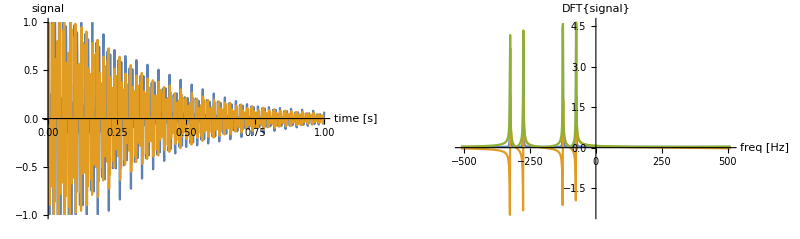

```mathematica
DFFT[Signal,t$List,True]
```

Let's plot the real, imaginary, and absolute value signals separately.  Notice how broad the imaginary-channel and absolute-value channel signals are.

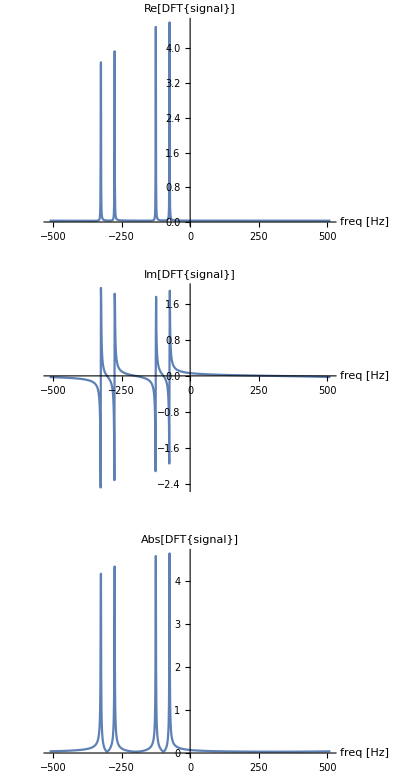

```mathematica
DFFT$all[Signal,t$List]
```

Recalculate the signal with the spin-spin coupling dialed to zero.  Note how the doublet pattern in the spectrum vanishes.

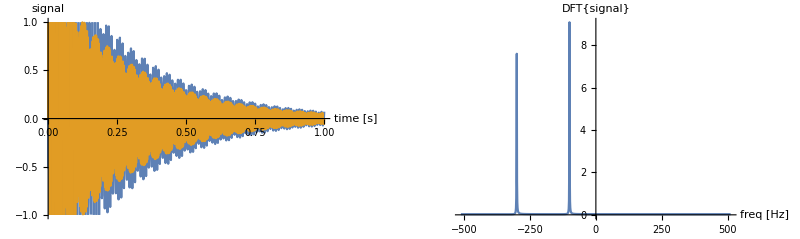

```mathematica
ρ = FreeEvolution[(Ix+Sx) ,t] Exp[-t/T2];
Signal[t_] = MakeNumerical[Tr[ρ**((Ix + Sx) + I (Iy + Sy))]] /. HamiltonianParameters$uncoupled;
DFFT[Signal,t$List,False]
```

Evolve just I_x.  We see just one of the doublets.

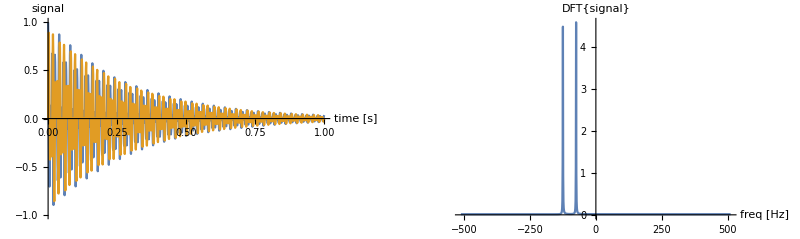

```mathematica
ρ = FreeEvolution[Ix ,t] Exp[-t/T2];
Signal[t_] = MakeNumerical[Tr[ρ**((Ix + Sx) + I (Iy + Sy))]]/. HamiltonianParameters$coupled;
DFFT[Signal,t$List,False]
```

Evolve just S_x.  See see just the other doublet.

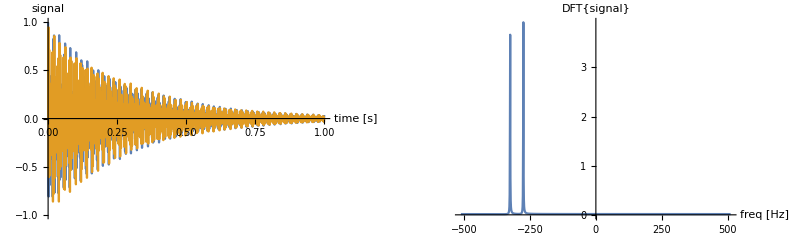

```mathematica
ρ = FreeEvolution[Sx ,t] Exp[-t/T2];
Signal[t_] = MakeNumerical[Tr[ρ**((Ix + Sx)+ I (Iy + Sy))]] /. HamiltonianParameters$coupled;
DFFT[Signal,t$List,False]
```

## INEPT polarization transfer

Here INEPT is an acronym that stands for insensitive nuclei enhanced by polarization transfer.  Thinking through the INEPT experiment helps you understand how two-dimensional spectroscopy works.  

The INEPT experiment shows how a J coupling can be harnessed to transfer spin polarization from a nucleus with a large magnetic moment -- ^1 H, the I-spin here -- to a nucleus with a small magnetic moment -- ^13 C, the S-spin here.  At thermal equilibrium the initial density operator is

	ρ_equil= a I_z+ b S_z
	
with a and b the Curie factors for each of the spins.  We worked through these Curie-law factors in detail on a homework.  To discuss the INEPT experiment it is enough to know that the factor b is about 1/16 the size of the a factor:

```mathematica
SubstitutePrefactors = {a -> 1,  b-> (1/4)^2};
```

In other words, the thermal-equilibrium ^13 C signal is about 1/16 as large as the thermal-equilibrium ^1 H signal in a magnetic resonance experiment.

### The usual ^13 C spectrum

Let’s calculate the usual ^13 C signal.  Deliver a π/2 pulse to the ^13 C spins and then evolve the spins under the Hamiltonian

	H =  Δ_I I_z+ Δ_S S_z + J I_z S_z
	
For simplicity we will work on resonance where Δ_I→0 and  Δ_S→0.

```mathematica
ρ$0  = a Iz + b Sz//  PulseS[#,π/2,π/2]&;
ρ$1 = FreeEvolution[ρ$0,t]/. {Δ$I-> 0,Δ$S-> 0}
```

a Iz+b (Sx Cos[(J t)/2]+2 Mult[Iz,Sy] Sin[(J t)/2])

We detect the complex magnetization and Fourier transform it to obtain the ^13 C spectrum.

```mathematica
Signal[t_] =(MakeNumerical[Tr[Mult[ρ$1,(Sx + I Sy)]] Exp[-t/T2]] /. HamiltonianParameters$coupled )/.SubstitutePrefactors
```

ⅇ^(-3.33333 t) (1/16 (-1/4 Cos[50 π t]-1/4 ⅈ Sin[50 π t])+3/16 (1/4 Cos[50 π t]-1/4 ⅈ Sin[50 π t])+1/16 (-1/4 Cos[50 π t]+1/4 ⅈ Sin[50 π t])+3/16 (1/4 Cos[50 π t]+1/4 ⅈ Sin[50 π t]))

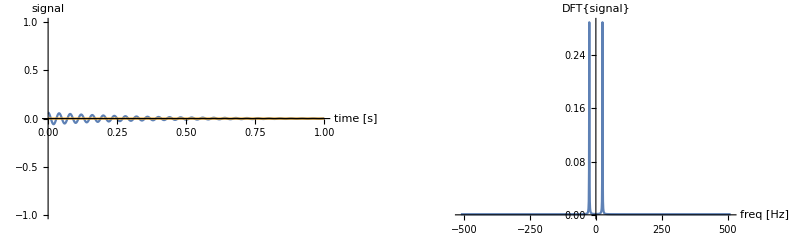

```mathematica
DFFT[Signal,t$List,False]
```

The spectrum shows a symmetric doublet, due the J-coupling, that is centered near zero frequency.  The height of each peak in the spectrum is approximately ~0.28.

### The ^13 C spectrum following polarization transfer from ^1 H

The INEPT experiment consists of a string of pulses applied to the I-spins and the S-spins.  

	 I spins: (π/2)_y-τ-(π)_x-τ-(π/2)_x
	S spins:                             (π)_x-τ-(π/2)_y-detect

with the time delay set to τ = 2π / (4 J), with J the scalar coupling.  Now let’s calculate the usual ^13 C signal following the INEPT polarization-transfer sequence.  For simplicity we will again work on resonance where Δ_I→0 and  Δ_S→0.  in the calculation below I print out the density operator at each step in the evolution.

```mathematica
ρ$0  = a Iz + b Sz//  PulseI[#,π/2,π/2]&
ρ$1 =  FreeEvolution[ρ$0,t] /. {Δ$I-> 0}
ρ$2 = ρ$1 //  PulseI[#,0,π]& //  PulseS[#,0,π] &
ρ$3 = FreeEvolution[ρ$2,t] /. {Δ$I-> 0} 
ρ$4 = ρ$3 //  PulseI[#,0,π/2]& //  PulseS[#,π/2,π/2] &
```

a Ix+b Sz

b Sz+a (Ix Cos[(J t)/2]+2 Mult[Iy,Sz] Sin[(J t)/2])

-b Sz+a (Ix Cos[(J t)/2]+2 Mult[Iy,Sz] Sin[(J t)/2])

-b Sz+a (2 Sin[(J t)/2] (Cos[(J t)/2] Mult[Iy,Sz]-1/2 Ix Sin[(J t)/2])+Cos[(J t)/2] (Ix Cos[(J t)/2]+2 Mult[Iy,Sz] Sin[(J t)/2]))

-b Sx+a (2 Sin[(J t)/2] (Cos[(J t)/2] Mult[Iz,Sx]-1/2 Ix Sin[(J t)/2])+Cos[(J t)/2] (Ix Cos[(J t)/2]+2 Mult[Iz,Sx] Sin[(J t)/2]))

The signal in the “regular” experiment arose from the term 

	b Sx Cos[(J t)/2] 
	
in the density operator.  After the series of pulses in the INEPT experiment we now have a term in the density operator given by 

	4 a Cos[(J t)/2] Iz Sx Sin[(J t)/2]→2 a Iz Sx

where the term following the arrow is what we get by setting the delay time to 2 π/(4 J).    This term arose from the initial I-spin signal evolving under the spin-spin coupling to give a mixed I-spin & S-spin signal.  Further evolution under the J coupling Hamiltonian will give rise a a pure S-spin signal.

```mathematica
ρ$5 = ρ$4  /. {t-> 2 π/(4 J)} // FreeEvolution[#,t]&
```

-b (Cos[(J t)/2] (Sx Cos[t Δ$S]+Sy Sin[t Δ$S])+2 Sin[(J t)/2] (Cos[t Δ$S] Mult[Iz,Sy]-Mult[Iz,Sx] Sin[t Δ$S]))+a (√2 (-1/(2 √2)(Cos[(J t)/2] (Ix Cos[t Δ$I]+Iy Sin[t Δ$I])+2 Sin[(J t)/2] (Cos[t Δ$I] Mult[Iy,Sz]-Mult[Ix,Sz] Sin[t Δ$I]))+1/(√2)(2 Sin[(J t)/2] (1/4 Sy Cos[t Δ$S]-1/4 Sx Sin[t Δ$S])+Cos[(J t)/2] (Cos[t Δ$S] Mult[Iz,Sx]+Mult[Iz,Sy] Sin[t Δ$S])))+1/(√2)(1/(√2)(Cos[(J t)/2] (Ix Cos[t Δ$I]+Iy Sin[t Δ$I])+2 Sin[(J t)/2] (Cos[t Δ$I] Mult[Iy,Sz]-Mult[Ix,Sz] Sin[t Δ$I]))+√2 (2 Sin[(J t)/2] (1/4 Sy Cos[t Δ$S]-1/4 Sx Sin[t Δ$S])+Cos[(J t)/2] (Cos[t Δ$S] Mult[Iz,Sx]+Mult[Iz,Sy] Sin[t Δ$S]))))

Remarkably, the ^13 C signal is now approximately 16x larger.  This signal increase corresponds to a 16^2= 256-fold savings in signal averaging time.

```mathematica
Signal[t_] = (MakeNumerical[Tr[ρ$5.(Sx + I Sy)] Exp[-t/T2]]/. {Δ$I-> 0,Δ$S-> 0}) /. HamiltonianParameters$coupled /. SubstitutePrefactors
```

ⅇ^(-3.33333 t) (-1/16 Cos[50 π t]+ⅈ Sin[50 π t])

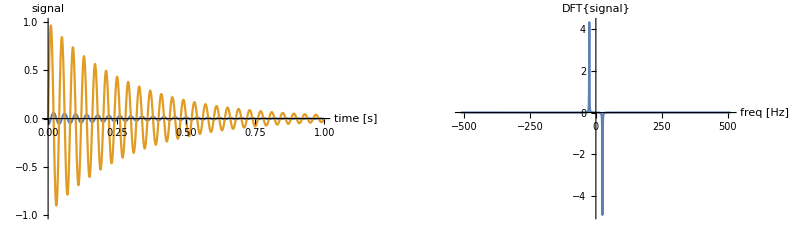

```mathematica
DFFT[Signal,t$List,False]
```

## Utility functions for two-dimensional data

### Function to take the 2D Fourier Transform

```mathematica
DFFT2[signal_,t1_, t2_, query_:False] :=

 (* signal = A function that computes the signal *)
 (*     t1 = A list of time points *)
 (*     t2 = A list of time points *)
 (*  query = True or False, whether to print out diagnostic messages *) 

Module[{t1$NN, (* number of time points in the indirect, t1 dimension *)
             t2$NN,  (* number of time points in the direct, t2 dimension *)
             f1,         (* the frequency axis in the indirect dimension *)
             f2             (* the frequency axis in the indirect dimension *)
},

(* Too fancy: signal$List = Outer[N[signal[#1,#2]]&,t1,t2]; *)

t1$NN = Dimensions[t1][[1]];
t2$NN = Dimensions[t2][[1]];

signal$List  = Table[signal[t1[[i$1]],t2[[i$2]]] // N,{i$2,1,t2$NN},{i$1,1,t1$NN}];

If[query == True,
Print["Number of t1 points = ",t1$NN];
Print["Number of t2 points = ",t2$NN];
Print["Dimensions of signal$List = ",Dimensions[signal$List ]];
];

signal$List$FT = RotateLeft[Fourier[signal$List ],{t2$NN/2,t1$NN/2}];

f1 = Table[jj/t1[[-1]],{jj,-t1$NN/2,t1$NN/2-1}];
f2 = Table[jj/t2[[-1]],{jj,-t2$NN/2,t2$NN/2-1}];

SetOptions[ListPlot3D,
PlotRange->All,
DataRange->{{f1[[1]],f1[[t1$NN]]},{f2[[1]],f2[[t2$NN]]}},
PlotLabel->"2D spectrum\n\n",
Mesh->False];

p1=ListPlot3D[Re[signal$List$FT ],
AxesLabel->{"f1 [Hz]","f2 [Hz]","Re[FT[signal(t_1,t_2)]]"},
ViewPoint->{1.561,-2.881,0.845}];

p2=ListPlot3D[Im[signal$List$FT ],
AxesLabel->{"f1 [Hz]","f2 [Hz]","Im[FT[signal(t_1,t_2)]]"},
ViewPoint->{1.561,-2.881,0.845}];

p3=ListPlot3D[Abs[signal$List$FT ],
AxesLabel->{"f1 [Hz]","f2 [Hz]","Abs[FT[signal(t_1,t_2)]]"},
ViewPoint->{1.561,-2.881,0.845}];

Return[{p1,p2,p3}]
]
```

### Test case #1

```mathematica
t1$List= TimeArray[2^6,0.25];
t2$List= TimeArray[2^7,0.50];
```

```mathematica
t1$List  // TimeArrayReport
t2$List  // TimeArrayReport
```

The time step is 0.00396825 s

The Nyquist frequency is 126. Hz

The time step is 0.00393701 s

The Nyquist frequency is 127. Hz

```mathematica
Signal2D[t1_,t2_] = Exp[-I 2 π 100 t1]  Exp[I 2 π 50 t2] Exp[-t1/0.08 ] Exp[-t2/0.15] + 0.05;
{p1,p2,p3} = DFFT2[Signal2D,t1$List,t2$List, True];

p3
```

Number of t1 points = 64

Number of t2 points = 128

Dimensions of signal$List = {128,64}

-Graphics3D-

### Test Case #2

```mathematica
t1$List= TimeArray[2^9,0.25];
t2$List= TimeArray[2^6,0.50];

t1$List  // TimeArrayReport
t2$List  // TimeArrayReport

Signal2D[t1_,t2_] = Exp[-I 2 π  300 t1]  Exp[-I 2 π  30 t2] Exp[-t1/0.05 ] Exp[-t2/0.10] + 0.05;
{p1,p2,p3} = DFFT2[Signal2D,t1$List,t2$List, True];

p3
```

The time step is 0.000489237 s

The Nyquist frequency is 1022. Hz

The time step is 0.00793651 s

The Nyquist frequency is 63. Hz

Number of t1 points = 512

Number of t2 points = 64

Dimensions of signal$List = {64,512}

-Graphics3D-

## Heteronuclear COSY signal

This is the signal that we worked out in class

### Set the couplings and number of points

Edit the chemical shifts and the J-couplings here

```mathematica
HamiltonianParameters$coupled =

{Δ$I-> 2π * 100, (* I-spin chemical shift [radians] *)
Δ$S -> 2π *150,  (* S-spin chemical shift [radians] *)
J ->2π * 40,        (* scalar coupling [radians] *)
T2 -> 0.10             (* spin dephasing time [s] *)
 };
```

Edit the number of points at the total acquisition time here

```mathematica
t1$List= TimeArray[2^7,0.25];
t2$List= TimeArray[2^7,0.25];
```

Make a copy of the parameters with the scalar coupling set to zero, e.g., with the two spins uncoupled.  Useful for testing.

```mathematica
HamiltonianParameters$uncoupled = HamiltonianParameters$coupled;
HamiltonianParameters$uncoupled[[3]]  = J-> 0;
```

### Some checks

Check out the Nyquist frequencies

```mathematica
t1$List  // TimeArrayReport
t2$List  // TimeArrayReport
```

The time step is 0.0019685 s

The Nyquist frequency is 254. Hz

The time step is 0.0019685 s

The Nyquist frequency is 254. Hz

### Evolve the density operator

Compute evolution.  This computation takes many seconds.

```mathematica
ρ$0 = Iz+ Sz;

(* Initial (π/2)y pulse*)

ρ$1$A = ρ$0 // PulseS[#,π/2,π/2]&  // Expand
ρ$2$A = FreeEvolution[ρ$1$A,t1] // Expand
ρ$3$A = ρ$2$A  // PulseS[#,π/2,π/2]& // PulseI[#,π/2,π/2]&  // Expand
ρ$4$A =FreeEvolution[ ρ$3$A ,t2] /. Mult-> SortedMult // Expand (* /. Mult -> MultSort *)

(* Initial (π/2)x pulse*)

ρ$1$B = ρ$0 // PulseS[#,0,π/2]&
ρ$2$B =FreeEvolution[ρ$1$B,t1];
ρ$3$B = ρ$2$B  // PulseS[#,π/2,π/2]& // PulseI[#,π/2,π/2]&// Expand
ρ$4$B =FreeEvolution[ρ$3$B,t2] /. Mult-> SortedMult// Expand (* /. Mult -> MultSort *)
```

Iz+Sx

Iz+Sx Cos[(J t1)/2] Cos[t1 Δ$S]+2 Cos[t1 Δ$S] Mult[Iz,Sy] Sin[(J t1)/2]+Sy Cos[(J t1)/2] Sin[t1 Δ$S]-2 Mult[Iz,Sx] Sin[(J t1)/2] Sin[t1 Δ$S]

Ix-Sz Cos[(J t1)/2] Cos[t1 Δ$S]+2 Cos[t1 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2]+Sy Cos[(J t1)/2] Sin[t1 Δ$S]+2 Mult[Ix,Sz] Sin[(J t1)/2] Sin[t1 Δ$S]

Ix Cos[(J t2)/2] Cos[t2 Δ$I]-Sz Cos[(J t1)/2] Cos[t1 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2]+2 Cos[t2 Δ$I] Mult[Iy,Sz] Sin[(J t2)/2]+2 Cos[t2 Δ$I] Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2+Iy Cos[(J t2)/2] Sin[t2 Δ$I]+2 Cos[(J t2)/2]^2 Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Iy,Sy] Sin[(J t1)/2] Sin[t2 Δ$I]-2 Mult[Ix,Sz] Sin[(J t2)/2] Sin[t2 Δ$I]+2 Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Iy,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I]+Sy Cos[(J t1)/2] Cos[(J t2)/2] Cos[t2 Δ$S] Sin[t1 Δ$S]+2 Cos[(J t2)/2] Cos[t2 Δ$I] Mult[Ix,Sz] Sin[(J t1)/2] Sin[t1 Δ$S]-2 Cos[(J t1)/2] Cos[t2 Δ$S] Mult[Iz,Sx] Sin[(J t2)/2] Sin[t1 Δ$S]+Iy Cos[t2 Δ$I] Sin[(J t1)/2] Sin[(J t2)/2] Sin[t1 Δ$S]+2 Cos[(J t2)/2] Mult[Iy,Sz] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t1 Δ$S]-Ix Sin[(J t1)/2] Sin[(J t2)/2] Sin[t2 Δ$I] Sin[t1 Δ$S]-2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Cos[t1 Δ$S] Mult[Ix,Sx] Sin[(J t1)/2] Sin[t2 Δ$S]-2 Cos[t2 Δ$I] Cos[t1 Δ$S] Mult[Ix,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Cos[t1 Δ$S] Mult[Iy,Sx] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t2 Δ$S]-2 Cos[t1 Δ$S] Mult[Iy,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I] Sin[t2 Δ$S]-Sx Cos[(J t1)/2] Cos[(J t2)/2] Sin[t1 Δ$S] Sin[t2 Δ$S]-2 Cos[(J t1)/2] Mult[Iz,Sy] Sin[(J t2)/2] Sin[t1 Δ$S] Sin[t2 Δ$S]

Iz-Sy

Ix-Sy Cos[(J t1)/2] Cos[t1 Δ$S]-2 Cos[t1 Δ$S] Mult[Ix,Sz] Sin[(J t1)/2]-Sz Cos[(J t1)/2] Sin[t1 Δ$S]+2 Mult[Ix,Sy] Sin[(J t1)/2] Sin[t1 Δ$S]

Ix Cos[(J t2)/2] Cos[t2 Δ$I]-Sy Cos[(J t1)/2] Cos[(J t2)/2] Cos[t1 Δ$S] Cos[t2 Δ$S]-2 Cos[(J t2)/2] Cos[t2 Δ$I] Cos[t1 Δ$S] Mult[Ix,Sz] Sin[(J t1)/2]+2 Cos[t2 Δ$I] Mult[Iy,Sz] Sin[(J t2)/2]+2 Cos[(J t1)/2] Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Iz,Sx] Sin[(J t2)/2]-Iy Cos[t2 Δ$I] Cos[t1 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2]+Iy Cos[(J t2)/2] Sin[t2 Δ$I]-2 Cos[(J t2)/2] Cos[t1 Δ$S] Mult[Iy,Sz] Sin[(J t1)/2] Sin[t2 Δ$I]-2 Mult[Ix,Sz] Sin[(J t2)/2] Sin[t2 Δ$I]+Ix Cos[t1 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2] Sin[t2 Δ$I]-Sz Cos[(J t1)/2] Sin[t1 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2] Sin[t1 Δ$S]+2 Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$S] Mult[Iy,Sy] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t1 Δ$S]+2 Cos[t2 Δ$S] Mult[Iy,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I] Sin[t1 Δ$S]+Sx Cos[(J t1)/2] Cos[(J t2)/2] Cos[t1 Δ$S] Sin[t2 Δ$S]+2 Cos[(J t1)/2] Cos[t1 Δ$S] Mult[Iz,Sy] Sin[(J t2)/2] Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Mult[Ix,Sx] Sin[(J t1)/2] Sin[t1 Δ$S] Sin[t2 Δ$S]-2 Cos[t2 Δ$I] Mult[Ix,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$S] Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Mult[Iy,Sx] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t1 Δ$S] Sin[t2 Δ$S]-2 Mult[Iy,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I] Sin[t1 Δ$S] Sin[t2 Δ$S]

### Examine the two signals and combine them

```mathematica
MakeNumerical[Tr[Mult[ρ$4$A,(Ix + I Iy)]]] // FullSimplify
```

ⅇ^(ⅈ t2 Δ$I) (Cos[(J t2)/2]+ⅈ Sin[(J t1)/2] Sin[(J t2)/2] Sin[t1 Δ$S])

```mathematica
MakeNumerical[Tr[Mult[ρ$4$B,(Ix + I Iy)]]]//  FullSimplify
```

ⅇ^(ⅈ t2 Δ$I) (Cos[(J t2)/2]-ⅈ Cos[t1 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2])

```mathematica
ρ$4 = ρ$4$A + ρ$4$B;
MakeNumerical[Tr[Mult[ρ$4,(Ix + I Iy)]]]  // FullSimplify // Expand
```

2 ⅇ^(ⅈ t2 Δ$I) Cos[(J t2)/2]-ⅈ ⅇ^(ⅈ t2 Δ$I) Cos[t1 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2]+ⅈ ⅇ^(ⅈ t2 Δ$I) Sin[(J t1)/2] Sin[(J t2)/2] Sin[t1 Δ$S]

### Compute the signal and apply the 2D FT

This computation should just take a few seconds.

```mathematica
Signal2D[t1_,t2_] = (MakeNumerical[Tr[Mult[ρ$4,(Ix + I Iy)]]] Exp[-t1/T2] Exp[-t2/T2] +0.025) /. 
HamiltonianParameters$coupled // Simplify // N;
```

Fourier transform the signal.   This takes a minute or so.

```mathematica
{p1,p2,p3} = DFFT2[Signal2D,t1$List,t2$List];
```

```mathematica
p1
p3
```

-Graphics3D-

-Graphics3D-

## Homonuclear COSY signal

This is the signal you get if you pulse and detect both nuclei at the same time.

### Set the couplings and number of points

Edit the chemical shifts and the J-couplings here

```mathematica
HamiltonianParameters$coupled =

{Δ$I-> 2π * 50, (* I-spin chemical shift [radians] *)
Δ$S -> 2π *150,  (* S-spin chemical shift [radians] *)
J ->2π * 23,        (* scalar coupling [radians] *)
T2 -> 0.10              (* spin dephasing time [s] *)
 };
```

Edit the number of points at the total acquisition time here

```mathematica
t1$List= TimeArray[2^7,0.25];
t2$List= TimeArray[2^7,0.25];
```

Make a copy of the parameters with the scalar coupling set to zero, e.g., with the two spins uncoupled.  Useful for testing.

```mathematica
HamiltonianParameters$uncoupled = HamiltonianParameters$coupled;
HamiltonianParameters$uncoupled[[3]]  = J-> 0;
```

### Some checks

Check out the Nyquist frequencies

```mathematica
t1$List  // TimeArrayReport
t2$List  // TimeArrayReport
```

The time step is 0.0019685 s

The Nyquist frequency is 254. Hz

The time step is 0.0019685 s

The Nyquist frequency is 254. Hz

### Evolve the density operator

Compute evolution.  This computation can take up to a minute.

```mathematica
ρ$0 = Iz+ Sz;

(* Initial (π/2)y pulses*)

ρ$1$A = (ρ$0 // PulseS[#,π/2,π/2]& // PulseI[#,π/2,π/2]&) // Expand 
ρ$2$A = FreeEvolution[ρ$1$A,t1]// Expand
ρ$3$A =( ρ$2$A  // PulseS[#,π/2,π/2]& // PulseI[#,π/2,π/2]& )// Expand
ρ$4$A = FreeEvolution[ρ$3$A,t2]// Expand /. Mult-> SortedMult

(* Initial (π/2)x pulses*)

ρ$1$B =( ρ$0 // PulseS[#,0,π/2]& //  PulseI[#,0,π/2]& ) // Expand 
ρ$2$B = FreeEvolution[ρ$1$B ,t1]// Expand 
ρ$3$B = (ρ$2$B  // PulseS[#,π/2,π/2]& // PulseI[#,π/2,π/2]& )// Expand 
ρ$4$B = FreeEvolution[ρ$3$B,t2]// Expand /. Mult-> SortedMult
```

Ix+Sx

Ix Cos[(J t1)/2] Cos[t1 Δ$I]+Sx Cos[(J t1)/2] Cos[t1 Δ$S]+2 Cos[t1 Δ$I] Mult[Iy,Sz] Sin[(J t1)/2]+2 Cos[t1 Δ$S] Mult[Iz,Sy] Sin[(J t1)/2]+Iy Cos[(J t1)/2] Sin[t1 Δ$I]-2 Mult[Ix,Sz] Sin[(J t1)/2] Sin[t1 Δ$I]+Sy Cos[(J t1)/2] Sin[t1 Δ$S]-2 Mult[Iz,Sx] Sin[(J t1)/2] Sin[t1 Δ$S]

-Iz Cos[(J t1)/2] Cos[t1 Δ$I]-Sz Cos[(J t1)/2] Cos[t1 Δ$S]+2 Cos[t1 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2]+2 Cos[t1 Δ$I] Mult[Iy,Sx] Sin[(J t1)/2]+Iy Cos[(J t1)/2] Sin[t1 Δ$I]+2 Mult[Iz,Sx] Sin[(J t1)/2] Sin[t1 Δ$I]+Sy Cos[(J t1)/2] Sin[t1 Δ$S]+2 Mult[Ix,Sz] Sin[(J t1)/2] Sin[t1 Δ$S]

-Iz Cos[(J t1)/2] Cos[t1 Δ$I]-Sz Cos[(J t1)/2] Cos[t1 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2]+2 Cos[(J t2)/2]^2 Cos[t1 Δ$I] Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Iy,Sx] Sin[(J t1)/2]-8 Cos[t1 Δ$I] Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Ix,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2-8 Cos[t2 Δ$I] Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Iy,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2+Iy Cos[(J t1)/2] Cos[(J t2)/2] Cos[t2 Δ$I] Sin[t1 Δ$I]+2 Cos[(J t2)/2] Cos[t2 Δ$S] Mult[Iz,Sx] Sin[(J t1)/2] Sin[t1 Δ$I]-2 Cos[(J t1)/2] Cos[t2 Δ$I] Mult[Ix,Sz] Sin[(J t2)/2] Sin[t1 Δ$I]+Sy Cos[t2 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2] Sin[t1 Δ$I]-2 Cos[(J t2)/2]^2 Cos[t1 Δ$I] Cos[t2 Δ$S] Mult[Ix,Sx] Sin[(J t1)/2] Sin[t2 Δ$I]+2 Cos[(J t2)/2]^2 Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Iy,Sy] Sin[(J t1)/2] Sin[t2 Δ$I]+8 Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Ix,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I]-8 Cos[t1 Δ$I] Cos[t2 Δ$S] Mult[Iy,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I]-Ix Cos[(J t1)/2] Cos[(J t2)/2] Sin[t1 Δ$I] Sin[t2 Δ$I]-2 Cos[(J t1)/2] Mult[Iy,Sz] Sin[(J t2)/2] Sin[t1 Δ$I] Sin[t2 Δ$I]+Sy Cos[(J t1)/2] Cos[(J t2)/2] Cos[t2 Δ$S] Sin[t1 Δ$S]+2 Cos[(J t2)/2] Cos[t2 Δ$I] Mult[Ix,Sz] Sin[(J t1)/2] Sin[t1 Δ$S]-2 Cos[(J t1)/2] Cos[t2 Δ$S] Mult[Iz,Sx] Sin[(J t2)/2] Sin[t1 Δ$S]+Iy Cos[t2 Δ$I] Sin[(J t1)/2] Sin[(J t2)/2] Sin[t1 Δ$S]+2 Cos[(J t2)/2] Mult[Iy,Sz] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t1 Δ$S]-Ix Sin[(J t1)/2] Sin[(J t2)/2] Sin[t2 Δ$I] Sin[t1 Δ$S]-2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Cos[t1 Δ$S] Mult[Ix,Sx] Sin[(J t1)/2] Sin[t2 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t1 Δ$I] Cos[t2 Δ$I] Mult[Iy,Sy] Sin[(J t1)/2] Sin[t2 Δ$S]+8 Cos[t1 Δ$I] Cos[t2 Δ$I] Mult[Ix,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$S]-8 Cos[t2 Δ$I] Cos[t1 Δ$S] Mult[Iy,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$S]+2 Cos[(J t2)/2] Mult[Iz,Sy] Sin[(J t1)/2] Sin[t1 Δ$I] Sin[t2 Δ$S]-Sx Sin[(J t1)/2] Sin[(J t2)/2] Sin[t1 Δ$I] Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Cos[t1 Δ$I] Mult[Ix,Sy] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Cos[t1 Δ$S] Mult[Iy,Sx] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t2 Δ$S]+8 Cos[t1 Δ$S] Mult[Ix,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I] Sin[t2 Δ$S]+8 Cos[t1 Δ$I] Mult[Iy,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I] Sin[t2 Δ$S]-Sx Cos[(J t1)/2] Cos[(J t2)/2] Sin[t1 Δ$S] Sin[t2 Δ$S]-2 Cos[(J t1)/2] Mult[Iz,Sy] Sin[(J t2)/2] Sin[t1 Δ$S] Sin[t2 Δ$S]

-Iy-Sy

-Iy Cos[(J t1)/2] Cos[t1 Δ$I]-Sy Cos[(J t1)/2] Cos[t1 Δ$S]+2 Cos[t1 Δ$I] Mult[Ix,Sz] Sin[(J t1)/2]+2 Cos[t1 Δ$S] Mult[Iz,Sx] Sin[(J t1)/2]+Ix Cos[(J t1)/2] Sin[t1 Δ$I]+2 Mult[Iy,Sz] Sin[(J t1)/2] Sin[t1 Δ$I]+Sx Cos[(J t1)/2] Sin[t1 Δ$S]+2 Mult[Iz,Sy] Sin[(J t1)/2] Sin[t1 Δ$S]

-Iy Cos[(J t1)/2] Cos[t1 Δ$I]-Sy Cos[(J t1)/2] Cos[t1 Δ$S]-2 Cos[t1 Δ$S] Mult[Ix,Sz] Sin[(J t1)/2]-2 Cos[t1 Δ$I] Mult[Iz,Sx] Sin[(J t1)/2]-Iz Cos[(J t1)/2] Sin[t1 Δ$I]+2 Mult[Iy,Sx] Sin[(J t1)/2] Sin[t1 Δ$I]-Sz Cos[(J t1)/2] Sin[t1 Δ$S]+2 Mult[Ix,Sy] Sin[(J t1)/2] Sin[t1 Δ$S]

-Iy Cos[(J t1)/2] Cos[(J t2)/2] Cos[t1 Δ$I] Cos[t2 Δ$I]-Sy Cos[(J t1)/2] Cos[(J t2)/2] Cos[t1 Δ$S] Cos[t2 Δ$S]-2 Cos[(J t2)/2] Cos[t2 Δ$I] Cos[t1 Δ$S] Mult[Ix,Sz] Sin[(J t1)/2]-2 Cos[(J t2)/2] Cos[t1 Δ$I] Cos[t2 Δ$S] Mult[Iz,Sx] Sin[(J t1)/2]+2 Cos[(J t1)/2] Cos[t1 Δ$I] Cos[t2 Δ$I] Mult[Ix,Sz] Sin[(J t2)/2]+2 Cos[(J t1)/2] Cos[t1 Δ$S] Cos[t2 Δ$S] Mult[Iz,Sx] Sin[(J t2)/2]-Iy Cos[t2 Δ$I] Cos[t1 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2]-Sy Cos[t1 Δ$I] Cos[t2 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2]-Iz Cos[(J t1)/2] Sin[t1 Δ$I]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Iy,Sx] Sin[(J t1)/2] Sin[t1 Δ$I]-8 Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Ix,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$I]+Ix Cos[(J t1)/2] Cos[(J t2)/2] Cos[t1 Δ$I] Sin[t2 Δ$I]-2 Cos[(J t2)/2] Cos[t1 Δ$S] Mult[Iy,Sz] Sin[(J t1)/2] Sin[t2 Δ$I]+2 Cos[(J t1)/2] Cos[t1 Δ$I] Mult[Iy,Sz] Sin[(J t2)/2] Sin[t2 Δ$I]+Ix Cos[t1 Δ$S] Sin[(J t1)/2] Sin[(J t2)/2] Sin[t2 Δ$I]-2 Cos[(J t2)/2]^2 Cos[t2 Δ$S] Mult[Ix,Sx] Sin[(J t1)/2] Sin[t1 Δ$I] Sin[t2 Δ$I]-8 Cos[t2 Δ$S] Mult[Iy,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$I] Sin[t2 Δ$I]-Sz Cos[(J t1)/2] Sin[t1 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Ix,Sy] Sin[(J t1)/2] Sin[t1 Δ$S]-8 Cos[t2 Δ$I] Cos[t2 Δ$S] Mult[Iy,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$S] Mult[Iy,Sy] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t1 Δ$S]+8 Cos[t2 Δ$S] Mult[Ix,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I] Sin[t1 Δ$S]+Sx Cos[(J t1)/2] Cos[(J t2)/2] Cos[t1 Δ$S] Sin[t2 Δ$S]-2 Cos[(J t2)/2] Cos[t1 Δ$I] Mult[Iz,Sy] Sin[(J t1)/2] Sin[t2 Δ$S]+2 Cos[(J t1)/2] Cos[t1 Δ$S] Mult[Iz,Sy] Sin[(J t2)/2] Sin[t2 Δ$S]+Sx Cos[t1 Δ$I] Sin[(J t1)/2] Sin[(J t2)/2] Sin[t2 Δ$S]+2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Mult[Iy,Sy] Sin[(J t1)/2] Sin[t1 Δ$I] Sin[t2 Δ$S]+8 Cos[t2 Δ$I] Mult[Ix,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$I] Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Mult[Ix,Sy] Sin[(J t1)/2] Sin[t1 Δ$I] Sin[t2 Δ$I] Sin[t2 Δ$S]+8 Mult[Iy,Sz,Iz,Sx] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$I] Sin[t2 Δ$I] Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Cos[t2 Δ$I] Mult[Ix,Sx] Sin[(J t1)/2] Sin[t1 Δ$S] Sin[t2 Δ$S]-8 Cos[t2 Δ$I] Mult[Iy,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t1 Δ$S] Sin[t2 Δ$S]-2 Cos[(J t2)/2]^2 Mult[Iy,Sx] Sin[(J t1)/2] Sin[t2 Δ$I] Sin[t1 Δ$S] Sin[t2 Δ$S]+8 Mult[Ix,Sz,Iz,Sy] Sin[(J t1)/2] Sin[(J t2)/2]^2 Sin[t2 Δ$I] Sin[t1 Δ$S] Sin[t2 Δ$S]

### Examine the two signals and combine them

```mathematica
MakeNumerical[Tr[Mult[ρ$4$A,((Ix + Sx) + I (Iy + Sy))]]]  // Simplify
```

ⅈ (Cos[(J t1)/2] Cos[(J t2)/2] (Cos[t2 Δ$I] Sin[t1 Δ$I]+ⅈ Sin[t1 Δ$I] Sin[t2 Δ$I]+Sin[t1 Δ$S] (Cos[t2 Δ$S]+ⅈ Sin[t2 Δ$S]))+Sin[(J t1)/2] Sin[(J t2)/2] (Cos[t2 Δ$S] Sin[t1 Δ$I]+Cos[t2 Δ$I] Sin[t1 Δ$S]+ⅈ (Sin[t2 Δ$I] Sin[t1 Δ$S]+Sin[t1 Δ$I] Sin[t2 Δ$S])))

```mathematica
MakeNumerical[Tr[Mult[ρ$4$B,((Ix + Sx) + I (Iy + Sy))]]]// Simplify
```

Sin[(J t1)/2] Sin[(J t2)/2] (-ⅈ Cos[t2 Δ$I] Cos[t1 Δ$S]+Cos[t1 Δ$S] Sin[t2 Δ$I]+Cos[t1 Δ$I] (-ⅈ Cos[t2 Δ$S]+Sin[t2 Δ$S]))+Cos[(J t1)/2] Cos[(J t2)/2] (Cos[t1 Δ$I] (-ⅈ Cos[t2 Δ$I]+Sin[t2 Δ$I])+Cos[t1 Δ$S] (-ⅈ Cos[t2 Δ$S]+Sin[t2 Δ$S]))

```mathematica
ρ$4 = -ρ$4$A + I ρ$4$B;
MakeNumerical[Tr[Mult[ρ$4,((Ix + Sx) + I (Iy + Sy))]]]// Simplify
```

Sin[(J t1)/2] Sin[(J t2)/2] (-ⅈ Cos[t2 Δ$S] Sin[t1 Δ$I]+ⅈ Cos[t1 Δ$S] Sin[t2 Δ$I]+Cos[t2 Δ$I] (Cos[t1 Δ$S]-ⅈ Sin[t1 Δ$S])+Sin[t2 Δ$I] Sin[t1 Δ$S]+Cos[t1 Δ$I] (Cos[t2 Δ$S]+ⅈ Sin[t2 Δ$S])+Sin[t1 Δ$I] Sin[t2 Δ$S])+2 Cos[(J t1)/2] Cos[(J t2)/2] Cos[1/2 (t1-t2) (Δ$I-Δ$S)] (Cos[1/2 (t1-t2) (Δ$I+Δ$S)]-ⅈ Sin[1/2 (t1-t2) (Δ$I+Δ$S)])

### Compute the signal and apply the 2D FT

This computation takes a minute .

```mathematica
Signal2D[t1_,t2_] = 
ReplaceAll[Times[MakeNumerical[Tr[Mult[ρ$4 ,((Ix + Sx) + I (Iy + Sy))]]],Exp[-t1/T2] Exp[-t2/T2]],HamiltonianParameters$coupled];
```

Fourier transform the signal.   This takes a couple of seconds.

```mathematica
{p1,p2,p3} = DFFT2[Signal2D,t1$List,t2$List];
```

```mathematica
p3
```

-Graphics3D-